## The Laplace Transform and Applications Section 7.2

## Example 1

```mathematica
IVP:=y'[t]-y[t]== 2Cos[3t]
```

```mathematica
Gensol:= DSolve[IVP, y[t], t]
```

```mathematica
Gensol
```

{{y[t]→ⅇ^t C[1]+1/5 (-Cos[3 t]+3 Sin[3 t])}}

```mathematica
parsol:=DSolve[{IVP,y[0]==1}, y[t], t]
```

```mathematica
parsol
```

{{y[t]→1/5 (6 ⅇ^t-Cos[3 t]+3 Sin[3 t])}}

```mathematica
{{y[t]->1/5 (6 ⅇ^t-Cos[3 t]+3 Sin[3 t])}}
```

{{y[t]→1/5 (6 ⅇ^t-Cos[3 t]+3 Sin[3 t])}}

```mathematica
y[t]/.parsol[[1]]
```

1/5 (6 ⅇ^t-Cos[3 t]+3 Sin[3 t])

```mathematica
TeXForm[%]
```

TexForm[1/5 (6 ⅇ^t-Cos[3 t]+3 Sin[3 t])]

## Example 2

```mathematica
IVP:=y''[t]-5y'[t]+4y[t] ==t
```

```mathematica
Gensol:= DSolve[IVP, y, t]
```

```mathematica
Gensol
```

{{y→Function[{t},1/16 (5+4 t)+ⅇ^t C[1]+ⅇ^(4 t) C[2]]}}

```mathematica
parsol:=DSolve[{IVP,y[0]==1, y'[0]==0}, y, t]
```

```mathematica
parsol
```

{{y→Function[{t},1/16 (5+16 ⅇ^t-5 ⅇ^(4 t)+4 t)]}}

```mathematica
y[t]/.parsol[[1]]
```

1/16 (5+16 ⅇ^t-5 ⅇ^(4 t)+4 t)

```mathematica
Distribute[%]
```

5/16+ⅇ^t-(5 ⅇ^(4 t))/16+t/4

```mathematica
TeXForm[%]
```

\frac{t}{4}+e^t-\frac{5 e^{4 t}}{16}+\frac{5}{16}

```mathematica
Plot[y[t]/. parsol,{t,-1,2}]
```

DSolve::dsvar: -0.999939 cannot be used as a variable.

ReplaceAll::reps: {DSolve[{4 y[-0.999939]-5 y'[-0.999939]+y''[-0.999939]==-0.999939,y[0]==1,y'[0]==0},y,-0.999939]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DSolve::dsvar: -0.999939 cannot be used as a variable.

ReplaceAll::reps: {DSolve[{4. y[-0.999939]-5. y'[-0.999939]+y''[-0.999939]==-0.999939,y[0.]==1.,y'[0.]==0.},y,-0.999939]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DSolve::dsvar: -0.938714 cannot be used as a variable.

General::stop: Further output of DSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {DSolve[{4 y[-0.938714]-5 y'[-0.938714]+y''[-0.938714]==-0.938714,y[0]==1,y'[0]==0},y,-0.938714]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
y[0]/.parsol[[1]]
```

1

```mathematica
x[t]:=y[t]/.Gensol[[1]]
```

```mathematica
x[t]
```

1/16 (5+4 t)+ⅇ^t C[1]+ⅇ^(4 t) C[2]

```mathematica
Plot[x[t], {t, 0, 2}]
```

-Graphics-

## Exercises

## 1. (i)

-y[t]+y'[t]==1

-y[t]+y'[t]==1

y[0]==0

{{y→Function[{t},-1+ⅇ^t C[1]]}}

{{y→Function[{t},-1+ⅇ^t]}}

True

0

1

{-1+ⅇ^t}

{-1+ⅇ^t}

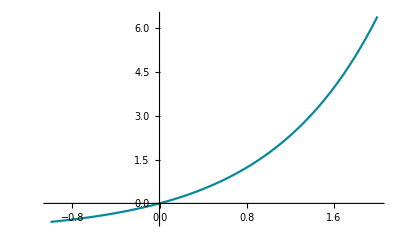

\left\{e^t-1\right\}

```mathematica
Clear[t, x, y]
DE=y'[t]-y[t]==1
DE
IC=y[0]==0
Gensol=DSolve[DE,y,t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Expand[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,2}]
```

## (ii)

-6 y[t]+y'[t]==ⅇ^(2 t)

-6 y[t]+y'[t]==ⅇ^(2 t)

y[0]==1

{{y→Function[{t},-ⅇ^(2 t)/4+ⅇ^(6 t) C[1]]}}

{{y→Function[{t},1/4 ⅇ^(2 t) (-1+5 ⅇ^(4 t))]}}

True

1

7

{1/4 ⅇ^(2 t) (-1+5 ⅇ^(4 t))}

{-ⅇ^(2 t)/4+(5 ⅇ^(6 t))/4}

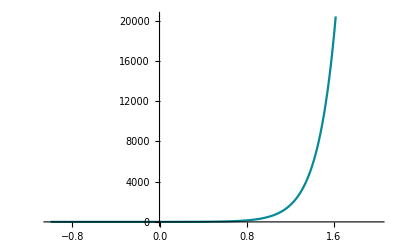

\left\{\frac{5 e^{6 t}}{4}-\frac{e^{2 t}}{4}\right\}

```mathematica
Clear[t, x, y]
DE=y'[t]-6*y[t]==Exp[2*t]
DE
IC=y[0]==1
Gensol=DSolve[DE,y,t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Expand[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,2}]
```

## (iii)

{{y→Function[{t},ⅇ^(2 t)/20+ⅇ^(-3 t) C[1]+ⅇ^(-2 t) C[2]]}}

{y[0]==1,y'[0]==0}

{{y→Function[{t},1/20 ⅇ^(-3 t) (-36+55 ⅇ^t+ⅇ^(5 t))]}}

True

1

0

{1/20 ⅇ^(-3 t) (-36+55 ⅇ^t+ⅇ^(5 t))}

{-9/5 ⅇ^(-3 t)+(11 ⅇ^(-2 t))/4+ⅇ^(2 t)/20}

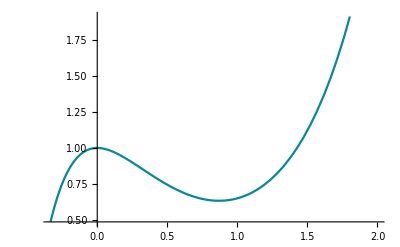

\left\{-\frac{9}{5} e^{-3 t}+\frac{11 e^{-2 t}}{4}+\frac{e^{2 t}}{20}\right\}

```mathematica
Clear[t, x, y]
linearsecondorderODE=y''[t]+5*y'[t]+6*y[t]==Exp[2*t];
generalsolution=DSolve[linearsecondorderODE,y,t]
IC={y[0]==1, y'[0]==0}
particularsolution=DSolve[{linearsecondorderODE,IC},y,t]
linearsecondorderODE/. particularsolution[[1]]//Simplify
y[0]/. particularsolution[[1]]
y'[0]/. particularsolution[[1]]
y[t]/. particularsolution
Expand[%]
TeXForm[%]
Plot[y[t]/. particularsolution,{t,-1/3,2}]
```

{{y→Function[{t},1/20 ⅇ^(-3 t) (-36-20 a+55 ⅇ^t+20 a ⅇ^t+ⅇ^(5 t))]}}

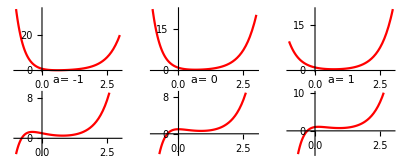

```mathematica
particularsolution = 
 DSolve[{linearsecondorderODE, y[0] == 1, y'[0] == a}, y, t]
 Show[GraphicsGrid[
  Partition[
   Table[Plot[
     Evaluate[y[t] /. particularsolution[[1]] /. a -> i], {t, -1, 3}, 
     PlotStyle -> {Red}, PlotLabel -> StringJoin["a= ", ToString[i]], 
     Ticks -> None], {i, -4, 1}], {3}], ImageSize -> 400]]
```

## (iv)

{{y→Function[{t},ⅇ^(2 t)/20+ⅇ^(-3 t) C[1]+ⅇ^(-2 t) C[2]]}}

{y[0]==0,y'[0]==1}

{{y→Function[{t},1/20 ⅇ^(-3 t) (-16+15 ⅇ^t+ⅇ^(5 t))]}}

True

0

1

{1/20 ⅇ^(-3 t) (-16+15 ⅇ^t+ⅇ^(5 t))}

{-4/5 ⅇ^(-3 t)+(3 ⅇ^(-2 t))/4+ⅇ^(2 t)/20}

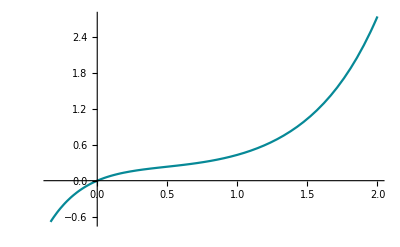

\left\{-\frac{4}{5} e^{-3 t}+\frac{3 e^{-2 t}}{4}+\frac{e^{2 t}}{20}\right\}

```mathematica
Clear[t, x, y]
linearsecondorderODE=y''[t]+5*y'[t]+6*y[t]==Exp[2*t];
generalsolution=DSolve[linearsecondorderODE,y,t]
IC={y[0]==0, y'[0]==1}
particularsolution=DSolve[{linearsecondorderODE,IC},y,t]
linearsecondorderODE/. particularsolution[[1]]//Simplify
y[0]/. particularsolution[[1]]
y'[0]/. particularsolution[[1]]
y[t]/. particularsolution
Expand[%]
TeXForm[%]
Plot[y[t]/. particularsolution,{t,-1/3,2}]
```

## (v)

9 y[t]+y''[t]==ⅇ^(2 t)

{y[0]==0,y'[0]==1}

{{y→Function[{t},C[1] Cos[3 t]+C[2] Sin[3 t]+1/13 ⅇ^(2 t) (Cos[3 t]^2+Sin[3 t]^2)]}}

{{y→Function[{t},1/39 (-3 Cos[3 t]+3 ⅇ^(2 t) Cos[3 t]^2+11 Sin[3 t]+3 ⅇ^(2 t) Sin[3 t]^2)]}}

True

0

1

{1/39 (-3 Cos[3 t]+3 ⅇ^(2 t) Cos[3 t]^2+11 Sin[3 t]+3 ⅇ^(2 t) Sin[3 t]^2)}

{-1/13 Cos[3 t]+1/13 ⅇ^(2 t) Cos[3 t]^2+11/39 Sin[3 t]+1/13 ⅇ^(2 t) Sin[3 t]^2}

{1/39 (3 ⅇ^(2 t)-3 Cos[3 t]+11 Sin[3 t])}

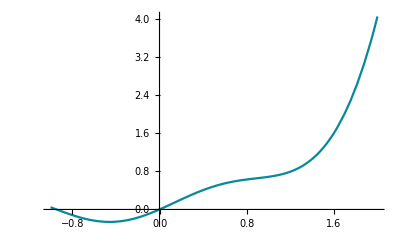

\left\{\frac{1}{39} \left(3 e^{2 t}+11 \sin (3 t)-3 \cos (3 t)\right)\right\}

```mathematica
Clear[t, x, y]
DE=y''[t]+9*y[t]==Exp[2*t]
IC={y[0]==0, y'[0]==1}
Gensol=DSolve[DE,y,t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Expand[%]
Simplify[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,2}]
```

## 2.

## (i)

y[t]+y'[t]==ⅇ^(3 t) Sin[2 t]

y[t]+y'[t]==ⅇ^(3 t) Sin[2 t]

y[0]==0

{{y→Function[{t},ⅇ^-t C[1]-1/10 ⅇ^(3 t) (Cos[2 t]-2 Sin[2 t])]}}

{{y→Function[{t},-1/10 ⅇ^-t (-1+ⅇ^(4 t) Cos[2 t]-2 ⅇ^(4 t) Sin[2 t])]}}

True

0

0

{-1/10 ⅇ^-t (-1+ⅇ^(4 t) Cos[2 t]-2 ⅇ^(4 t) Sin[2 t])}

{ⅇ^-t/10-1/10 ⅇ^(3 t) Cos[2 t]+1/5 ⅇ^(3 t) Sin[2 t]}

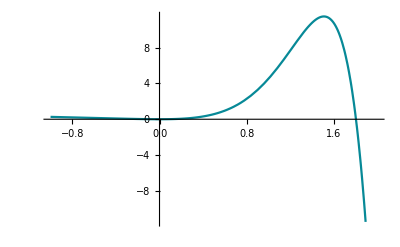

\left\{\frac{e^{-t}}{10}+\frac{1}{5} e^{3 t} \sin (2 t)-\frac{1}{10} e^{3 t} \cos (2 t)\right\}

```mathematica
Clear[t, x, y]
DE=y'[t]+y[t]==Exp[3*t]*Sin[2*t]
DE
IC=y[0]==0
Gensol=DSolve[DE,y,t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Expand[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,2}]
```

## (ii)

5 y[t]-4 y'[t]+y''[t]==0

5 y[t]-4 y'[t]+y''[t]==0

{{y→Function[{t},ⅇ^(2 t) C[2] Cos[t]+ⅇ^(2 t) C[1] Sin[t]]}}

{{y→Function[{t},ⅇ^(2 t) (Cos[t]-Sin[t])]}}

True

1

1

{ⅇ^(2 t) (Cos[t]-Sin[t])}

{ⅇ^(2 t) Cos[t]-ⅇ^(2 t) Sin[t]}

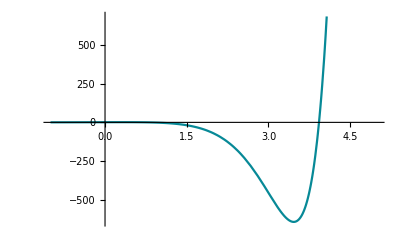

\left\{e^{2 t} \cos (t)-e^{2 t} \sin (t)\right\}

```mathematica
Clear[Derivative]
DE=y''[t]-4y'[t]+5y[t]==0
DE
Gensol=DSolve[DE,y,t]
Parsol=DSolve[{DE,y[0]==1, y'[0]==1},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Expand[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1, 5}]
```

(iii)

-y'[t]+y''[t]==ⅇ^t Sin[t]

{y[0]==0,y'[0]==0}

{{y→Function[{t},1/2 (-1+2 ⅇ^t-ⅇ^t Cos[t]-ⅇ^t Sin[t])]}}

{{y→Function[{t},1/2 (-1+2 ⅇ^t-ⅇ^t Cos[t]-ⅇ^t Sin[t])]}}

True

0

0

{1/2 (-1+2 ⅇ^t-ⅇ^t Cos[t]-ⅇ^t Sin[t])}

{-1/2+ⅇ^t-1/2 ⅇ^t Cos[t]-1/2 ⅇ^t Sin[t]}

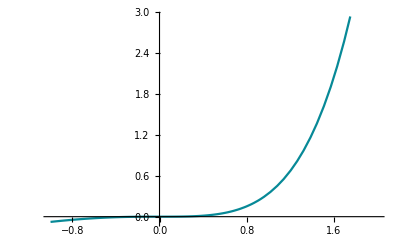

\left\{e^t-\frac{1}{2} e^t \sin (t)-\frac{1}{2} e^t \cos (t)-\frac{1}{2}\right\}

```mathematica
Clear[Derivative]
DE=y''[t]-y'[t] == Exp[t] Sin[t]
IC={y[0]==0, y'[0]==0}
Gensol = DSolve[{DE, IC}, y, t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Expand[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,2}]
```

## (iv)

```mathematica
Clear[x, y, t]
diffeq=y'''[t]+2y''[t]-y'[t]-2y[t] == Sin[t]
trasnformdeq=LaplaceTransform[diffeq, t,s]/. {y[0]->0,y'[0]->0, y''[0]->1,LaplaceTransform[y[t], t, s]->Y}
soln=Solve[trasnformdeq, Y]//Flatten
Y=Y/.soln
InverseLaplaceTransform[Y, s, t]
TeXForm[%]
```

-2 y[t]-y'[t]+2 y''[t]+y^(3)[t]==Sin[t]

Solve::ivar: (2+s^2)/((1+s^2) (-2-s+2 s^2+s^3)) is not a valid variable.

ReplaceAll::reps: {Solve[-1-(2 (2+s^2))/((1+Power[«2»]) (-2+Times[«2»]+Times[«2»]+Power[«2»]))-(s (2+s^2))/((1+Power[«2»]) (-2+Times[«2»]+Times[«2»]+Power[«2»]))+(2 s^2 (2+s^2))/((1+Power[«2»]) (-2+Times[«2»]+Times[«2»]+Power[«2»]))+(s^3 (2+s^2))/((1+Power[«2»]) (-2+Times[«2»]+Times[«2»]+Power[«2»]))==1/(1+s^2),(2+s^2)/((1+s^2) (-2-s+2 s^2+s^3))]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-1-2 ((2+s^2)/((1+s^2) (-2-s+2 s^2+s^3))/.Solve[-1-(2 (2+s^2))/((1+s^2) (-2-s+2 s^2+s^3))-(s (2+s^2))/((1+s^2) (-2-s+2 s^2+s^3))+(2 s^2 (2+s^2))/((1+s^2) (-2-s+2 s^2+s^3))+(s^3 (2+s^2))/((1+s^2) (-2-s+2 s^2+s^3))==1/(1+s^2),(2+s^2)/((1+s^2) (-2-s+2 s^2+s^3))])-s ((2+s^2)/((1+s^2) (-2-s+2 s^2+s^3))/.Solve[-1-(2 (2+s^2))/((1+s^2) (-2-s+2 s^2+s^3))-(s (2+s^2))/((1+s^2) (-2-s+2 s^2+s^3))+(2 s^2 (2+s^2))/((1+s^2) (-2-s+2 s^2+s^3))+(s^3 (2+s^2))/((1+s^2) (-2-s+2 s^2+s^3))==1/(1+s^2),(2+s^2)/((1+s^2) (-2-s+2 s^2+s^3))])+2 s^2 ((2+s^2)/((1+s^2) (-2-s+2 s^2+s^3))/.Solve[-1-(2 (2+s^2))/((1+s^2) (-2-s+2 s^2+s^3))-(s (2+s^2))/((1+s^2) (-2-s+2 s^2+s^3))+(2 s^2 (2+s^2))/((1+s^2) (-2-s+2 s^2+s^3))+(s^3 (2+s^2))/((1+s^2) (-2-s+2 s^2+s^3))==1/(1+s^2),(2+s^2)/((1+s^2) (-2-s+2 s^2+s^3))])+s^3 ((2+s^2)/((1+s^2) (-2-s+2 s^2+s^3))/.Solve[-1-(2 (2+s^2))/((1+s^2) (-2-s+2 s^2+s^3))-(s (2+s^2))/((1+s^2) (-2-s+2 s^2+s^3))+(2 s^2 (2+s^2))/((1+s^2) (-2-s+2 s^2+s^3))+(s^3 (2+s^2))/((1+s^2) (-2-s+2 s^2+s^3))==1/(1+s^2),(2+s^2)/((1+s^2) (-2-s+2 s^2+s^3))])==1/(1+s^2)

{((2+s^2)/((1+s^2) (-2-s+2 s^2+s^3))/.Solve[-1-(2 (2+s^2))/((1+s^2) (-2-s+2 s^2+s^3))-(s (2+s^2))/((1+s^2) (-2-s+2 s^2+s^3))+(2 s^2 (2+s^2))/((1+s^2) (-2-s+2 s^2+s^3))+(s^3 (2+s^2))/((1+s^2) (-2-s+2 s^2+s^3))==1/(1+s^2),(2+s^2)/((1+s^2) (-2-s+2 s^2+s^3))])→(2+s^2)/((1+s^2) (-2-s+2 s^2+s^3))}

(2+s^2)/((1+s^2) (-2-s+2 s^2+s^3))

1/20 (8 ⅇ^(-2 t)-15 ⅇ^-t+5 ⅇ^t+2 Cos[t]-4 Sin[t])

\frac{1}{20} \left(8 e^{-2 t}-15 e^{-t}+5 e^t-4 \sin (t)+2 \cos (t)\right)

-2 y[t]-y'[t]+2 y''[t]+y^(3)[t]==Sin[t]

{y[0]==0,y'[0]==0,y''[0]==1}

{{y→Function[{t},1/20 ⅇ^(-2 t) (8-15 ⅇ^t+5 ⅇ^(3 t)+2 ⅇ^(2 t) Cos[t]-4 ⅇ^(2 t) Sin[t])]}}

{{y→Function[{t},1/20 ⅇ^(-2 t) (8-15 ⅇ^t+5 ⅇ^(3 t)+2 ⅇ^(2 t) Cos[t]-4 ⅇ^(2 t) Sin[t])]}}

True

0

0

{1/20 ⅇ^(-2 t) (8-15 ⅇ^t+5 ⅇ^(3 t)+2 ⅇ^(2 t) Cos[t]-4 ⅇ^(2 t) Sin[t])}

{(2 ⅇ^(-2 t))/5-(3 ⅇ^-t)/4+ⅇ^t/4+Cos[t]/10-Sin[t]/5}

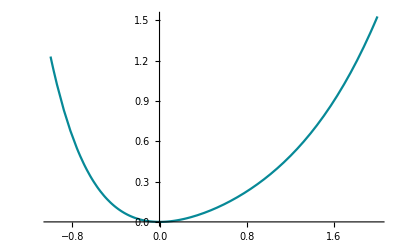

\left\{\frac{2 e^{-2 t}}{5}-\frac{3 e^{-t}}{4}+\frac{e^t}{4}-\frac{\sin (t)}{5}+\frac{\cos (t)}{10}\right\}

```mathematica
Clear[Derivative]
DE=y'''[t]+2y''[t]-y'[t]-2y[t] == Sin[t]
IC={y[0]==0, y'[0]==0, y''[0]==1}
Gensol = DSolve[{DE, IC}, y, t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Expand[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,2}]
```

## 3.

## (i) .

4 y[t]+y'[t]==1-2 UnitStep[-1+t]

{y[0]==0}

{{y→Function[{t},-1/4 ⅇ^(-4 t) (1-2 ⅇ^4+ⅇ^(4 t))+(1/4 ⅇ^(-4 t) (-1+ⅇ^(4 t))+1/4 ⅇ^(-4 t) (1-2 ⅇ^4+ⅇ^(4 t))) UnitStep[1-t]]}}

{{y→Function[{t},-1/4 ⅇ^(-4 t) (1-2 ⅇ^4+ⅇ^(4 t))+(1/4 ⅇ^(-4 t) (-1+ⅇ^(4 t))+1/4 ⅇ^(-4 t) (1-2 ⅇ^4+ⅇ^(4 t))) UnitStep[1-t]]}}

t≠1

1/4 (2-2 ⅇ^4)+1/4 (-2+2 ⅇ^4)

1

{-1/4 ⅇ^(-4 t) (1-2 ⅇ^4+ⅇ^(4 t))+(1/4 ⅇ^(-4 t) (-1+ⅇ^(4 t))+1/4 ⅇ^(-4 t) (1-2 ⅇ^4+ⅇ^(4 t))) UnitStep[1-t]}

{Piecewise[{{1/4-ⅇ^(-4 t)/4, t≤1}, {-1/4 ⅇ^(-4 t) (1-2 ⅇ^4+ⅇ^(4 t)), True}}]}

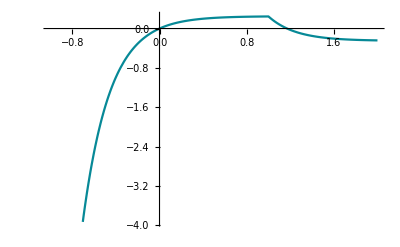

\left\{
\begin{array}{cc}
 \{ & 
\begin{array}{cc}
 \frac{1}{4}-\frac{e^{-4 t}}{4} & t\leq 1 \\
 -\frac{1}{4} e^{-4 t} \left(1-2 e^4+e^{4 t}\right) & \text{True} \\
\end{array}
 \\
\end{array}
\right\}

```mathematica
Clear[Derivative]
DE=y'[t]+4y[t] == 1- 2*UnitStep[t-1]
IC={y[0]==0}
Gensol = DSolve[{DE, IC}, y, t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Simplify[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,2}]
```

(ii) .

4 y[t]+y'[t]==Sin[t] (1-UnitStep[-1+t])

{y[0]==0}

{{y→Function[{t},-1/17 ⅇ^(-4 t) (-1+ⅇ^4 Cos[1]-4 ⅇ^4 Sin[1])+(1/17 ⅇ^(-4 t) (-1+ⅇ^4 Cos[1]-4 ⅇ^4 Sin[1])-1/17 ⅇ^(-4 t) (-1+ⅇ^(4 t) Cos[t]-4 ⅇ^(4 t) Sin[t])) UnitStep[1-t]]}}

{{y→Function[{t},-1/17 ⅇ^(-4 t) (-1+ⅇ^4 Cos[1]-4 ⅇ^4 Sin[1])+(1/17 ⅇ^(-4 t) (-1+ⅇ^4 Cos[1]-4 ⅇ^4 Sin[1])-1/17 ⅇ^(-4 t) (-1+ⅇ^(4 t) Cos[t]-4 ⅇ^(4 t) Sin[t])) UnitStep[1-t]]}}

t≠1

1/17 (-1+ⅇ^4 Cos[1]-4 ⅇ^4 Sin[1])+1/17 (1-ⅇ^4 Cos[1]+4 ⅇ^4 Sin[1])

-4/17 (-1+ⅇ^4 Cos[1]-4 ⅇ^4 Sin[1])-4/17 (1-ⅇ^4 Cos[1]+4 ⅇ^4 Sin[1])

{-1/17 ⅇ^(-4 t) (-1+ⅇ^4 Cos[1]-4 ⅇ^4 Sin[1])+(1/17 ⅇ^(-4 t) (-1+ⅇ^4 Cos[1]-4 ⅇ^4 Sin[1])-1/17 ⅇ^(-4 t) (-1+ⅇ^(4 t) Cos[t]-4 ⅇ^(4 t) Sin[t])) UnitStep[1-t]}

{Piecewise[{{1/17 ⅇ^(-4 t) (1-ⅇ^4 (Cos[1]-4 Sin[1])), t>1}, {1/17 (ⅇ^(-4 t)-Cos[t]+4 Sin[t]), True}}]}

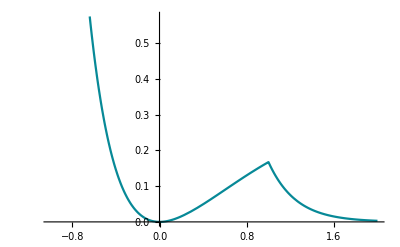

\left\{
\begin{array}{cc}
 \{ & 
\begin{array}{cc}
 \frac{1}{17} e^{-4 t} \left(1-e^4 (\cos (1)-4 \sin (1))\right) & t>1 \\
 \frac{1}{17} \left(-\cos (t)+e^{-4 t}+4 \sin (t)\right) & \text{True} \\
\end{array}
 \\
\end{array}
\right\}

```mathematica
Clear[Derivative]
DE=y'[t]+4y[t] == Sin[t] *(1- UnitStep[t-1])
IC={y[0]==0}
Gensol = DSolve[{DE, IC}, y, t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Simplify[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,2}]
```

## Laplace transform method

```mathematica
Clear[x, y, t]
Clear[Derivative]
diffeq=y'[t]+4y[t] == Sin[t] *(1- UnitStep[t-1])
trasnformdeq=LaplaceTransform[diffeq, t,s]/. {y[0]->0,LaplaceTransform[y[t], t, s]->Y}
soln=Solve[trasnformdeq, Y]//Flatten
Y=Y/.soln
InverseLaplaceTransform[Y, s, t]
Simplify[%]
TeXForm[%]
```

4 y[t]+y'[t]==Sin[t] (1-UnitStep[-1+t])

Solve::ivar: (ⅇ^(-2 π s) (-1+ⅇ^(2 π s)))/((4+s) (1+s^2)) is not a valid variable.

ReplaceAll::reps: {Solve[(4 ⅇ^(-2 π s) (-1+ⅇ^Times[«3»]))/((4+s) (1+Power[«2»]))+(ⅇ^(-2 π s) (-1+ⅇ^Times[«3»]) s)/((4+s) (1+Power[«2»]))==1/(1+s^2)-(ⅇ^-s (Cos[1]+s Sin[«1»]))/(1+Power[«2»]),(ⅇ^(-2 π s) (-1+ⅇ^(2 π s)))/((4+s) (1+s^2))]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

4 ((ⅇ^(-2 π s) (-1+ⅇ^(2 π s)))/((4+s) (1+s^2))/.Solve[(4 ⅇ^(-2 π s) (-1+ⅇ^(2 π s)))/((4+s) (1+s^2))+(ⅇ^(-2 π s) (-1+ⅇ^(2 π s)) s)/((4+s) (1+s^2))==1/(1+s^2)-(ⅇ^-s (Cos[1]+s Sin[1]))/(1+s^2),(ⅇ^(-2 π s) (-1+ⅇ^(2 π s)))/((4+s) (1+s^2))])+s ((ⅇ^(-2 π s) (-1+ⅇ^(2 π s)))/((4+s) (1+s^2))/.Solve[(4 ⅇ^(-2 π s) (-1+ⅇ^(2 π s)))/((4+s) (1+s^2))+(ⅇ^(-2 π s) (-1+ⅇ^(2 π s)) s)/((4+s) (1+s^2))==1/(1+s^2)-(ⅇ^-s (Cos[1]+s Sin[1]))/(1+s^2),(ⅇ^(-2 π s) (-1+ⅇ^(2 π s)))/((4+s) (1+s^2))])==1/(1+s^2)-(ⅇ^-s (Cos[1]+s Sin[1]))/(1+s^2)

{((ⅇ^(-2 π s) (-1+ⅇ^(2 π s)))/((4+s) (1+s^2))/.Solve[(4 ⅇ^(-2 π s) (-1+ⅇ^(2 π s)))/((4+s) (1+s^2))+(ⅇ^(-2 π s) (-1+ⅇ^(2 π s)) s)/((4+s) (1+s^2))==1/(1+s^2)-(ⅇ^-s (Cos[1]+s Sin[1]))/(1+s^2),(ⅇ^(-2 π s) (-1+ⅇ^(2 π s)))/((4+s) (1+s^2))])→(ⅇ^-s (ⅇ^s-Cos[1]-s Sin[1]))/((4+s) (1+s^2))}

(ⅇ^-s (ⅇ^s-Cos[1]-s Sin[1]))/((4+s) (1+s^2))

ⅇ^(-4 t)/17-Cos[1] HeavisideTheta[-1+t] (1/17 ⅇ^(-4 (-1+t))+1/17 (-Cos[1-t]-4 Sin[1-t]))-HeavisideTheta[-1+t] Sin[1] (-4/17 ⅇ^(-4 (-1+t))+1/17 (4 Cos[1-t]-Sin[1-t]))+1/17 (-Cos[t]+4 Sin[t])

1/17 ⅇ^(-4 t) (1-ⅇ^(4 t) Cos[t]+4 ⅇ^(4 t) Sin[t]+HeavisideTheta[-1+t] (ⅇ^(4 t) Cos[t]-ⅇ^4 (Cos[1]-4 Sin[1])-4 ⅇ^(4 t) Sin[t]))

\frac{1}{17} e^{-4 t} \left(\theta (t-1) \left(-4 e^{4 t} \sin (t)+e^{4 t} \cos (t)-e^4 (\cos (1)-4 \sin (1))\right)+4 e^{4 t} \sin (t)-e^{4 t} \cos (t)+1\right)

(iii) .

-y'[t]+y''[t]==Cos[t] UnitStep[-2 π+t]

{y[0]==1,y'[0]==1}

{{y→Function[{t},1/2 ⅇ^(-2 π) (ⅇ^t+2 ⅇ^(2 π+t)-ⅇ^(2 π) Cos[t]-ⅇ^(2 π) Sin[t])+(ⅇ^t-1/2 ⅇ^(-2 π) (ⅇ^t+2 ⅇ^(2 π+t)-ⅇ^(2 π) Cos[t]-ⅇ^(2 π) Sin[t])) UnitStep[2 π-t]]}}

{{y→Function[{t},1/2 ⅇ^(-2 π) (ⅇ^t+2 ⅇ^(2 π+t)-ⅇ^(2 π) Cos[t]-ⅇ^(2 π) Sin[t])+(ⅇ^t-1/2 ⅇ^(-2 π) (ⅇ^t+2 ⅇ^(2 π+t)-ⅇ^(2 π) Cos[t]-ⅇ^(2 π) Sin[t])) UnitStep[2 π-t]]}}

t≠2 π

1

1

{1/2 ⅇ^(-2 π) (ⅇ^t+2 ⅇ^(2 π+t)-ⅇ^(2 π) Cos[t]-ⅇ^(2 π) Sin[t])+(ⅇ^t-1/2 ⅇ^(-2 π) (ⅇ^t+2 ⅇ^(2 π+t)-ⅇ^(2 π) Cos[t]-ⅇ^(2 π) Sin[t])) UnitStep[2 π-t]}

{Piecewise[{{ⅇ^t, t≤2 π}, {1/2 (ⅇ^t (2+ⅇ^(-2 π))-Cos[t]-Sin[t]), True}}]}

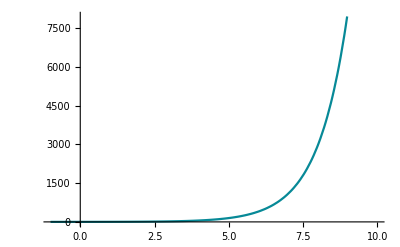

\left\{
\begin{array}{cc}
 \{ & 
\begin{array}{cc}
 e^t & t\leq 2 \pi  \\
 \frac{1}{2} \left(-\cos (t)-\sin (t)+e^t \left(2+e^{-2 \pi }\right)\right) & \text{True} \\
\end{array}
 \\
\end{array}
\right\}

```mathematica
Clear[Derivative]
DE=y''[t]-y'[t] == Cos[t]*UnitStep[t-2*Pi]
IC={y[0]==1, y'[0]==1}
Gensol = DSolve[{DE, IC}, y, t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Simplify[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,10}]
```

## Laplace Transform Method

```mathematica
Clear[x, y, t]
Clear[Derivative]
diffeq=y''[t]-y'[t] == Cos[t] *UnitStep[t-2*Pi]
trasnformdeq=LaplaceTransform[diffeq, t,s]/. {y[0]->1, y'[0]->1,LaplaceTransform[y[t], t, s]->Y}
soln=Solve[trasnformdeq, Y]//Flatten
Y=Y/.soln
InverseLaplaceTransform[Y, s, t]
Simplify[%]
TeXForm[%]
```

-y'[t]+y''[t]==Cos[t] UnitStep[-2 π+t]

Solve::ivar: (ⅇ^(-2 π s) s (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2)) is not a valid variable.

ReplaceAll::reps: {Solve[-s-(ⅇ^(-2 π s) s^2 (1+ⅇ^Times[«3»]+Power[«2»] Power[«2»]))/((1+Power[«2»]) (Times[«2»]+Power[«2»]))+(ⅇ^(-2 π s) s^3 (1+ⅇ^Times[«3»]+Power[«2»] Power[«2»]))/((1+Power[«2»]) (Times[«2»]+Power[«2»]))==(ⅇ^(-2 π s) s)/(1+s^2),(ⅇ^(-2 π s) s (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-s-s ((ⅇ^(-2 π s) s (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))/.Solve[-s-(ⅇ^(-2 π s) s^2 (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))+(ⅇ^(-2 π s) s^3 (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))==(ⅇ^(-2 π s) s)/(1+s^2),(ⅇ^(-2 π s) s (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))])+s^2 ((ⅇ^(-2 π s) s (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))/.Solve[-s-(ⅇ^(-2 π s) s^2 (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))+(ⅇ^(-2 π s) s^3 (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))==(ⅇ^(-2 π s) s)/(1+s^2),(ⅇ^(-2 π s) s (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))])==(ⅇ^(-2 π s) s)/(1+s^2)

{((ⅇ^(-2 π s) s (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))/.Solve[-s-(ⅇ^(-2 π s) s^2 (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))+(ⅇ^(-2 π s) s^3 (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))==(ⅇ^(-2 π s) s)/(1+s^2),(ⅇ^(-2 π s) s (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))])→(ⅇ^(-2 π s) s (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))}

(ⅇ^(-2 π s) s (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))

1/2 (ⅇ^t-Cos[t]-Sin[t])+1/2 HeavisideTheta[-2 π+t] (ⅇ^(-2 π+t)-Cos[t]-Sin[t])+1/2 (ⅇ^t+Cos[t]+Sin[t])

ⅇ^t+1/2 HeavisideTheta[-2 π+t] (ⅇ^(-2 π+t)-Cos[t]-Sin[t])

\frac{1}{2} \theta (t-2 \pi ) \left(e^{t-2 \pi }-\sin (t)-\cos (t)\right)+e^t

(iv) .

-y'[t]+y''[t]==Cos[t] UnitStep[-2 π+t]

{y[0]==0,y'[0]==1}

{{y→Function[{t},1/2 ⅇ^(-2 π) (-2 ⅇ^(2 π)+ⅇ^t+2 ⅇ^(2 π+t)-ⅇ^(2 π) Cos[t]-ⅇ^(2 π) Sin[t])+(-1+ⅇ^t-1/2 ⅇ^(-2 π) (-2 ⅇ^(2 π)+ⅇ^t+2 ⅇ^(2 π+t)-ⅇ^(2 π) Cos[t]-ⅇ^(2 π) Sin[t])) UnitStep[2 π-t]]}}

{{y→Function[{t},1/2 ⅇ^(-2 π) (-2 ⅇ^(2 π)+ⅇ^t+2 ⅇ^(2 π+t)-ⅇ^(2 π) Cos[t]-ⅇ^(2 π) Sin[t])+(-1+ⅇ^t-1/2 ⅇ^(-2 π) (-2 ⅇ^(2 π)+ⅇ^t+2 ⅇ^(2 π+t)-ⅇ^(2 π) Cos[t]-ⅇ^(2 π) Sin[t])) UnitStep[2 π-t]]}}

t≠2 π

0

1

{1/2 ⅇ^(-2 π) (-2 ⅇ^(2 π)+ⅇ^t+2 ⅇ^(2 π+t)-ⅇ^(2 π) Cos[t]-ⅇ^(2 π) Sin[t])+(-1+ⅇ^t-1/2 ⅇ^(-2 π) (-2 ⅇ^(2 π)+ⅇ^t+2 ⅇ^(2 π+t)-ⅇ^(2 π) Cos[t]-ⅇ^(2 π) Sin[t])) UnitStep[2 π-t]}

{Piecewise[{{-1+ⅇ^t, t≤2 π}, {1/2 (-2+2 ⅇ^t+ⅇ^(-2 π+t)-Cos[t]-Sin[t]), True}}]}

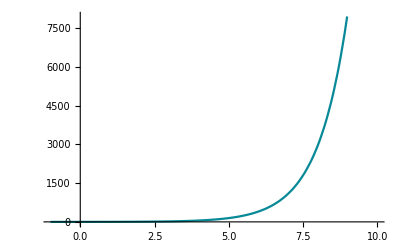

\left\{
\begin{array}{cc}
 \{ & 
\begin{array}{cc}
 -1+e^t & t\leq 2 \pi  \\
 \frac{1}{2} \left(-\cos (t)+2 e^t+e^{t-2 \pi }-\sin (t)-2\right) & \text{True} \\
\end{array}
 \\
\end{array}
\right\}

```mathematica
Clear[Derivative]
DE=y''[t]-y'[t] == Cos[t] *UnitStep[t-2*Pi]
IC={y[0]==0, y'[0]==1}
Gensol = DSolve[{DE, IC}, y, t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Simplify[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,10}]
```

## Laplace Transform Method

```mathematica
Clear[x, y, t]
Clear[Derivative]
diffeq=y''[t]-y'[t] == Cos[t] *UnitStep[t-2*Pi]
trasnformdeq=LaplaceTransform[diffeq, t,s]/. {y[0]->0, y'[0]->1,LaplaceTransform[y[t], t, s]->Y}
soln=Solve[trasnformdeq, Y]//Flatten
Y=Y/.soln
InverseLaplaceTransform[Y, s, t]
Simplify[%]
TeXForm[%]
```

-y'[t]+y''[t]==Cos[t] UnitStep[-2 π+t]

Solve::ivar: (ⅇ^(-2 π s) s (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2)) is not a valid variable.

ReplaceAll::reps: {Solve[-1-(ⅇ^(-2 π s) s^2 (1+ⅇ^Times[«3»]+Power[«2»] Power[«2»]))/((1+Power[«2»]) (Times[«2»]+Power[«2»]))+(ⅇ^(-2 π s) s^3 (1+ⅇ^Times[«3»]+Power[«2»] Power[«2»]))/((1+Power[«2»]) (Times[«2»]+Power[«2»]))==(ⅇ^(-2 π s) s)/(1+s^2),(ⅇ^(-2 π s) s (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-1-s ((ⅇ^(-2 π s) s (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))/.Solve[-1-(ⅇ^(-2 π s) s^2 (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))+(ⅇ^(-2 π s) s^3 (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))==(ⅇ^(-2 π s) s)/(1+s^2),(ⅇ^(-2 π s) s (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))])+s^2 ((ⅇ^(-2 π s) s (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))/.Solve[-1-(ⅇ^(-2 π s) s^2 (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))+(ⅇ^(-2 π s) s^3 (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))==(ⅇ^(-2 π s) s)/(1+s^2),(ⅇ^(-2 π s) s (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))])==(ⅇ^(-2 π s) s)/(1+s^2)

{((ⅇ^(-2 π s) s (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))/.Solve[-1-(ⅇ^(-2 π s) s^2 (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))+(ⅇ^(-2 π s) s^3 (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))==(ⅇ^(-2 π s) s)/(1+s^2),(ⅇ^(-2 π s) s (1+ⅇ^(2 π s)+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))])→(ⅇ^(-2 π s) (ⅇ^(2 π s)+s+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))}

(ⅇ^(-2 π s) (ⅇ^(2 π s)+s+ⅇ^(2 π s) s^2))/((1+s^2) (-s+s^2))

1/2 HeavisideTheta[-2 π+t] (ⅇ^(-2 π+t)-Cos[t]-Sin[t])+1/2 (-2+ⅇ^t+Cos[t]-Sin[t])+1/2 (ⅇ^t-Cos[t]+Sin[t])

-1+ⅇ^t+1/2 HeavisideTheta[-2 π+t] (ⅇ^(-2 π+t)-Cos[t]-Sin[t])

\frac{1}{2} \theta (t-2 \pi ) \left(e^{t-2 \pi }-\sin (t)-\cos (t)\right)+e^t-1

(v) .

2 y[t]+3 y'[t]+y''[t]==1+UnitStep[-6+t]-UnitStep[-4+t]-UnitStep[-2+t]

{y[0]==0,y'[0]==0}

{{y→Function[{t},-1/2 ⅇ^(-2 t) (-1+ⅇ^2)^2 (1+ⅇ^2) (-1-ⅇ^2-ⅇ^4-ⅇ^6+2 ⅇ^t)+UnitStep[2-t] (1/2 ⅇ^(-2 t) (-1+ⅇ^t)^2-1/2 ⅇ^(-2 t) (-1+ⅇ^2) (-1-ⅇ^2+2 ⅇ^t) UnitStep[4-t])+(1/2 ⅇ^(-2 t) (-1+ⅇ^2)^2 (1+ⅇ^2) (-1-ⅇ^2-ⅇ^4-ⅇ^6+2 ⅇ^t)-1/2 ⅇ^(-2 t) (-1+ⅇ^4+ⅇ^8+2 ⅇ^t+ⅇ^(2 t)-2 ⅇ^(2+t)-2 ⅇ^(4+t))) UnitStep[6-t]+UnitStep[4-t] (1/2 ⅇ^(-2 t) (-1+ⅇ^2) (-1-ⅇ^2+2 ⅇ^t)+1/2 ⅇ^(-2 t) (-1+ⅇ^4+ⅇ^8+2 ⅇ^t+ⅇ^(2 t)-2 ⅇ^(2+t)-2 ⅇ^(4+t)) UnitStep[6-t])]}}

{{y→Function[{t},-1/2 ⅇ^(-2 t) (-1+ⅇ^2)^2 (1+ⅇ^2) (-1-ⅇ^2-ⅇ^4-ⅇ^6+2 ⅇ^t)+UnitStep[2-t] (1/2 ⅇ^(-2 t) (-1+ⅇ^t)^2-1/2 ⅇ^(-2 t) (-1+ⅇ^2) (-1-ⅇ^2+2 ⅇ^t) UnitStep[4-t])+(1/2 ⅇ^(-2 t) (-1+ⅇ^2)^2 (1+ⅇ^2) (-1-ⅇ^2-ⅇ^4-ⅇ^6+2 ⅇ^t)-1/2 ⅇ^(-2 t) (-1+ⅇ^4+ⅇ^8+2 ⅇ^t+ⅇ^(2 t)-2 ⅇ^(2+t)-2 ⅇ^(4+t))) UnitStep[6-t]+UnitStep[4-t] (1/2 ⅇ^(-2 t) (-1+ⅇ^2) (-1-ⅇ^2+2 ⅇ^t)+1/2 ⅇ^(-2 t) (-1+ⅇ^4+ⅇ^8+2 ⅇ^t+ⅇ^(2 t)-2 ⅇ^(2+t)-2 ⅇ^(4+t)) UnitStep[6-t])]}}

t<2||2<t<4||4<t<6||t>6

1/2 (-2+2 ⅇ^2+ⅇ^4-ⅇ^8)+1/2 (2-2 ⅇ^2-ⅇ^4+ⅇ^8)

1/2 (4-2 ⅇ^2-2 ⅇ^4)+1/2 (-4+2 ⅇ^2+2 ⅇ^4)

{-1/2 ⅇ^(-2 t) (-1+ⅇ^2)^2 (1+ⅇ^2) (-1-ⅇ^2-ⅇ^4-ⅇ^6+2 ⅇ^t)+UnitStep[2-t] (1/2 ⅇ^(-2 t) (-1+ⅇ^t)^2-1/2 ⅇ^(-2 t) (-1+ⅇ^2) (-1-ⅇ^2+2 ⅇ^t) UnitStep[4-t])+(1/2 ⅇ^(-2 t) (-1+ⅇ^2)^2 (1+ⅇ^2) (-1-ⅇ^2-ⅇ^4-ⅇ^6+2 ⅇ^t)-1/2 ⅇ^(-2 t) (-1+ⅇ^4+ⅇ^8+2 ⅇ^t+ⅇ^(2 t)-2 ⅇ^(2+t)-2 ⅇ^(4+t))) UnitStep[6-t]+UnitStep[4-t] (1/2 ⅇ^(-2 t) (-1+ⅇ^2) (-1-ⅇ^2+2 ⅇ^t)+1/2 ⅇ^(-2 t) (-1+ⅇ^4+ⅇ^8+2 ⅇ^t+ⅇ^(2 t)-2 ⅇ^(2+t)-2 ⅇ^(4+t)) UnitStep[6-t])}

{Piecewise[{{1/2 ⅇ^(-2 t) (-1+ⅇ^t)^2, t≤2}, {1/2 ⅇ^(-2 t) (-1+ⅇ^2) (-1-ⅇ^2+2 ⅇ^t), 2<t≤4}, {1/2 ⅇ^(-2 t) (-1+ⅇ^2)^2 (1+ⅇ^2) (1+ⅇ^2+ⅇ^4+ⅇ^6-2 ⅇ^t), t>6}, {-1/2 ⅇ^(-2 t) (-1+ⅇ^4+ⅇ^8+2 ⅇ^t+ⅇ^(2 t)-2 ⅇ^(2+t)-2 ⅇ^(4+t)), True}}]}

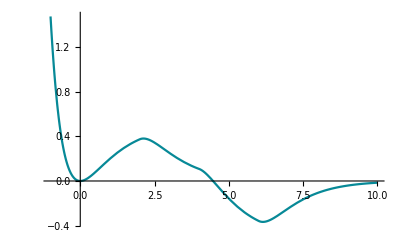

\left\{
\begin{array}{cc}
 \{ & 
\begin{array}{cc}
 \frac{1}{2} e^{-2 t} \left(-1+e^t\right)^2 & t\leq 2 \\
 \frac{1}{2} e^{-2 t} \left(-1+e^2\right) \left(-1-e^2+2 e^t\right) & 2<t\leq 4 \\
 \frac{1}{2} e^{-2 t} \left(-1+e^2\right)^2 \left(1+e^2\right) \left(1+e^2+e^4+e^6-2 e^t\right) & t>6 \\
 -\frac{1}{2} e^{-2 t} \left(-1+e^4+e^8+2 e^t+e^{2 t}-2 e^{t+2}-2 e^{t+4}\right) & \text{True} \\
\end{array}
 \\
\end{array}
\right\}

```mathematica
Clear[Derivative]
DE=y''[t]+3y'[t]+2y[t] == 1-UnitStep[t-2]-UnitStep[t-4]+UnitStep[t-6]
IC={y[0]==0, y'[0]==0}
Gensol = DSolve[{DE, IC}, y, t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Simplify[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,10}]
```

## Laplace Transform Method

```mathematica
Clear[x, t, y, y[t]]
Clear[Derivative]
diffeq=y''[t]+3y'[t]+2y[t] == 1-UnitStep[t-2]-UnitStep[t-4]+UnitStep[t-6]
trasnformdeq=LaplaceTransform[diffeq, t,s]/. {y[0]->0, y'[0]->0,LaplaceTransform[y[t], t, s]->Y}
soln=Solve[trasnformdeq, Y]//Flatten
Y=Y/.soln
InverseLaplaceTransform[Y, s, t]
Simplify[%]
TeXForm[%]
```

Clear::ssym: y[t] is not a symbol or a valid string pattern.

2 y[t]+3 y'[t]+y''[t]==1+UnitStep[-6+t]-UnitStep[-4+t]-UnitStep[-2+t]

Solve::ivar: (ⅇ^(-6 s) (-1+ⅇ^(2 s))^2 (1+ⅇ^(2 s)))/(s (3+4 s+s^2)) is not a valid variable.

ReplaceAll::reps: {Solve[(3 ⅇ^(-6 s) (-1+Power[«2»])^2 (1+ⅇ^Times[«2»]))/(3+Times[«2»]+Power[«2»])+(2 ⅇ^(-6 s) (-1+Power[«2»])^2 (1+ⅇ^Times[«2»]))/(s (3+Times[«2»]+Power[«2»]))+(ⅇ^(-6 s) (-1+Power[«2»])^2 (1+ⅇ^Times[«2»]) s)/(3+Times[«2»]+Power[«2»])==1/s+ⅇ^(-6 s)/s-ⅇ^(-4 s)/s-ⅇ^(-2 s)/s,(ⅇ^(-6 s) (-1+ⅇ^(2 s))^2 (1+ⅇ^(2 s)))/(s (3+4 s+s^2))]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

2 ((ⅇ^(-6 s) (-1+ⅇ^(2 s))^2 (1+ⅇ^(2 s)))/(s (3+4 s+s^2))/.Solve[(3 ⅇ^(-6 s) (-1+ⅇ^(2 s))^2 (1+ⅇ^(2 s)))/(3+4 s+s^2)+(2 ⅇ^(-6 s) (-1+ⅇ^(2 s))^2 (1+ⅇ^(2 s)))/(s (3+4 s+s^2))+(ⅇ^(-6 s) (-1+ⅇ^(2 s))^2 (1+ⅇ^(2 s)) s)/(3+4 s+s^2)==1/s+ⅇ^(-6 s)/s-ⅇ^(-4 s)/s-ⅇ^(-2 s)/s,(ⅇ^(-6 s) (-1+ⅇ^(2 s))^2 (1+ⅇ^(2 s)))/(s (3+4 s+s^2))])+3 s ((ⅇ^(-6 s) (-1+ⅇ^(2 s))^2 (1+ⅇ^(2 s)))/(s (3+4 s+s^2))/.Solve[(3 ⅇ^(-6 s) (-1+ⅇ^(2 s))^2 (1+ⅇ^(2 s)))/(3+4 s+s^2)+(2 ⅇ^(-6 s) (-1+ⅇ^(2 s))^2 (1+ⅇ^(2 s)))/(s (3+4 s+s^2))+(ⅇ^(-6 s) (-1+ⅇ^(2 s))^2 (1+ⅇ^(2 s)) s)/(3+4 s+s^2)==1/s+ⅇ^(-6 s)/s-ⅇ^(-4 s)/s-ⅇ^(-2 s)/s,(ⅇ^(-6 s) (-1+ⅇ^(2 s))^2 (1+ⅇ^(2 s)))/(s (3+4 s+s^2))])+s^2 ((ⅇ^(-6 s) (-1+ⅇ^(2 s))^2 (1+ⅇ^(2 s)))/(s (3+4 s+s^2))/.Solve[(3 ⅇ^(-6 s) (-1+ⅇ^(2 s))^2 (1+ⅇ^(2 s)))/(3+4 s+s^2)+(2 ⅇ^(-6 s) (-1+ⅇ^(2 s))^2 (1+ⅇ^(2 s)))/(s (3+4 s+s^2))+(ⅇ^(-6 s) (-1+ⅇ^(2 s))^2 (1+ⅇ^(2 s)) s)/(3+4 s+s^2)==1/s+ⅇ^(-6 s)/s-ⅇ^(-4 s)/s-ⅇ^(-2 s)/s,(ⅇ^(-6 s) (-1+ⅇ^(2 s))^2 (1+ⅇ^(2 s)))/(s (3+4 s+s^2))])==1/s+ⅇ^(-6 s)/s-ⅇ^(-4 s)/s-ⅇ^(-2 s)/s

{((ⅇ^(-6 s) (-1+ⅇ^(2 s))^2 (1+ⅇ^(2 s)))/(s (3+4 s+s^2))/.Solve[(3 ⅇ^(-6 s) (-1+ⅇ^(2 s))^2 (1+ⅇ^(2 s)))/(3+4 s+s^2)+(2 ⅇ^(-6 s) (-1+ⅇ^(2 s))^2 (1+ⅇ^(2 s)))/(s (3+4 s+s^2))+(ⅇ^(-6 s) (-1+ⅇ^(2 s))^2 (1+ⅇ^(2 s)) s)/(3+4 s+s^2)==1/s+ⅇ^(-6 s)/s-ⅇ^(-4 s)/s-ⅇ^(-2 s)/s,(ⅇ^(-6 s) (-1+ⅇ^(2 s))^2 (1+ⅇ^(2 s)))/(s (3+4 s+s^2))])→(ⅇ^(-6 s) (-1+ⅇ^(2 s))^2 (1+ⅇ^(2 s)))/(s (2+3 s+s^2))}

(ⅇ^(-6 s) (-1+ⅇ^(2 s))^2 (1+ⅇ^(2 s)))/(s (2+3 s+s^2))

1/2 ⅇ^(-2 t) (-1+ⅇ^t)^2+1/2 ⅇ^(-2 (-6+t)) (-1+ⅇ^(-6+t))^2 HeavisideTheta[-6+t]-1/2 ⅇ^(-2 (-4+t)) (-1+ⅇ^(-4+t))^2 HeavisideTheta[-4+t]-1/2 ⅇ^(-2 (-2+t)) (-1+ⅇ^(-2+t))^2 HeavisideTheta[-2+t]

1/2 ⅇ^(-2 t) (1-2 ⅇ^t+ⅇ^(2 t)+(ⅇ^6-ⅇ^t)^2 HeavisideTheta[-6+t]-(ⅇ^4-ⅇ^t)^2 HeavisideTheta[-4+t]-ⅇ^4 HeavisideTheta[-2+t]-ⅇ^(2 t) HeavisideTheta[-2+t]+2 ⅇ^(2+t) HeavisideTheta[-2+t])

\frac{1}{2} e^{-2 t} \left(\left(e^4-e^t\right)^2 (-\theta (t-4))+\left(e^6-e^t\right)^2 \theta (t-6)-e^{2 t} \theta (t-2)+2 e^{t+2} \theta (t-2)-e^4 \theta (t-2)-2 e^t+e^{2 t}+1\right)